```mathematica
nmax=2;
h=1;
w=1;
m=1;
psi[n_,x_]:=((m*w/(hbar*Pi))^(1/4)*1/Sqrt[2^n*n!]*HermiteH[n,Sqrt[m*w/hbar]*x]*Exp[-m*w*x^2/(2*hbar)])^2
```

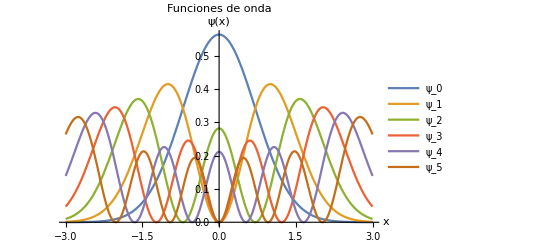

```mathematica
(*Set up parameters*)m=1;(*mass of the particle*)w=1;(*frequency of the oscillator*)hbar=1;(*Planck's constant/2pi*)nmax=5;(*maximum quantum number*)(*Define the wave function*)psi[n_,x_]:=(m*w/(hbar*Pi))^(1/4)*1/Sqrt[2^n*n!]*HermiteH[n,Sqrt[m*w/hbar]*x]*Exp[-m*w*x^2/(2*hbar)]

(*Plot the wave functions*)
Plot[Evaluate@Table[psi[n,x]^2,{n,0,nmax}],{x,-3,3},PlotRange->All,PlotStyle->Automatic,AxesLabel->{"x","ψ(x)"},PlotLegends->{"ψ_0","ψ_1","ψ_2","ψ_3","ψ_4","ψ_5"},PlotLabel->"Funciones de onda"]
```

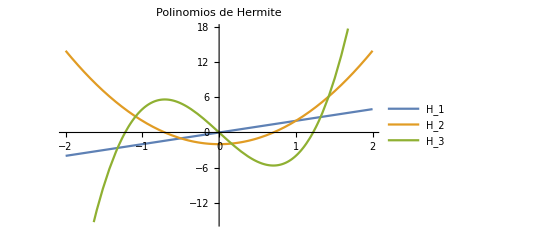

```mathematica
Plot[Evaluate[Table[HermiteH[n,x],{n,3}]],{x,-2,2},PlotLabel->"Polinomios de Hermite",PlotLegends->{"H_1","H_2","H_3"}]
```

```mathematica
Plot[x^3,{x^3,-2.5,2.5}]
```

$Failed

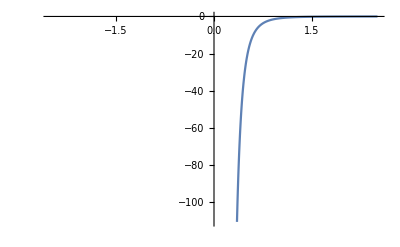

```mathematica
Plot[-x^-4.5,{x,-2.5,2.5}]
```